## 1. Optimal conditions and amplitude (*{R1^2->R1R1}*)

```mathematica
OptimalConditionI[g10_,h_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionII[g10_,KK_]=ϕ1^2-4*ϕ0*ϕ2;


OptimalConditionIII[g10_,phif_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionIV[g10_,cf_]=ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionV[g10_,beta_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVI[g10_,lamdaf_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVII[g10_,g30_]= ϕ1^2-4*ϕ0*ϕ2;

OptimalConditionVIII[g10_,c0_]= ϕ1^2-4*ϕ0*ϕ2;


OptimalCondition=ϕ1^2-4*ϕ0*ϕ2;
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;

amplitude=Amplitude/.{R1^2->R1R1};
```

## 2. parametric study for skin matrix

### 2.1 Relations of h and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;
cf=100;phif=0.05;lamdaf=0.885;g12=1;
beta=Pi/4;

hmin=10^-3;
hmax=5*10^-2;
samplePoints=Subdivide[hmin,hmax,49];
datahtestXZ=Table[{0,0,0,0,0},{h,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.12;
ninit=2.5;

For[i=Length[samplePoints],i>=1,i--,h=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at h = ",h];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datahtestXZ[[k]]={h,n,g10,Sqrt[R12]};
Print[{h,n,g10,Sqrt[R12]}];
k++;]


vdatahtestXZ=Select[datahtestXZ,#[[2]]>0&&#[[3]]>0&];
Maxg10htestXZ=Max[vdatahtestXZ[[All,3]]]
```

{1/20,2.59012,1.02911,0.606647}

{49/1000,2.63026,1.02881,0.594233}

{6/125,2.67187,1.02851,0.581929}

{47/1000,2.71502,1.02821,0.56973}

❌ FindRoot failed at h = 23/500

{9/200,2.80633,1.02759,0.545629}

{11/250,2.85471,1.02728,0.533719}

{43/1000,2.90504,1.02696,0.521896}

❌ FindRoot failed at h = 21/500

{41/1000,3.01214,1.02631,0.498497}

{1/25,3.06918,1.02599,0.486912}

{39/1000,3.12878,1.02565,0.475398}

{19/500,3.19112,1.02532,0.463952}

{37/1000,3.2564,1.02498,0.452568}

{9/250,3.32485,1.02463,0.441243}

{7/200,3.3967,1.02428,0.429973}

{17/500,3.47224,1.02393,0.418753}

{33/1000,3.55178,1.02357,0.40758}

{4/125,3.63565,1.0232,0.39645}

{31/1000,3.72424,1.02283,0.385357}

{3/100,3.81799,1.02245,0.374298}

{29/1000,3.91736,1.02207,0.363268}

{7/250,4.02293,1.02168,0.352263}

{27/1000,4.13531,1.02129,0.341278}

{13/500,4.25522,1.02088,0.330307}

{1/40,4.38349,1.02047,0.319346}

{3/125,4.52108,1.02005,0.308389}

{23/1000,4.66908,1.01963,0.29743}

{11/500,4.82879,1.01919,0.286463}

{21/1000,5.00175,1.01874,0.275481}

{1/50,5.18976,1.01829,0.264478}

{19/1000,5.39498,1.01782,0.253445}

{9/500,5.62003,1.01734,0.242375}

{17/1000,5.8681,1.01685,0.231257}

{2/125,6.14311,1.01634,0.220081}

{3/200,6.44996,1.01581,0.208837}

{7/500,6.79487,1.01527,0.197509}

{13/1000,7.1858,1.01471,0.186085}

{3/250,7.6332,1.01413,0.174545}

{11/1000,8.15105,1.01352,0.162868}

{1/100,8.75849,1.01289,0.151031}

{9/1000,9.48257,1.01222,0.139003}

{1/125,10.3628,1.01152,0.126746}

{7/1000,11.4595,1.01077,0.114211}

{3/500,12.8702,1.00997,0.101334}

{1/200,14.7637,1.0091,0.0880253}

{1/250,17.463,1.00813,0.0741539}

{3/1000,21.6818,1.00704,0.05951}

{1/500,29.4089,1.00574,0.0437114}

{1/1000,49.5051,1.00406,0.0258649}

1.02911

#### Graph

{1/20,1.02911,2.59012,0.606647,0.226831}

{49/1000,1.02881,2.63026,0.594233,0.222427}

{6/125,1.02851,2.67187,0.581929,0.218055}

{47/1000,1.02821,2.71502,0.56973,0.213715}

{9/200,1.02759,2.80633,0.545629,0.205123}

{11/250,1.02728,2.85471,0.533719,0.200868}

{43/1000,1.02696,2.90504,0.521896,0.196639}

{41/1000,1.02631,3.01214,0.498497,0.188249}

{1/25,1.02599,3.06918,0.486912,0.184086}

{39/1000,1.02565,3.12878,0.475398,0.179941}

{19/500,1.02532,3.19112,0.463952,0.175815}

{37/1000,1.02498,3.2564,0.452568,0.171704}

{9/250,1.02463,3.32485,0.441243,0.167608}

{7/200,1.02428,3.3967,0.429973,0.163525}

{17/500,1.02393,3.47224,0.418753,0.159453}

{33/1000,1.02357,3.55178,0.40758,0.155391}

{4/125,1.0232,3.63565,0.39645,0.151337}

{31/1000,1.02283,3.72424,0.385357,0.14729}

{3/100,1.02245,3.81799,0.374298,0.143247}

{29/1000,1.02207,3.91736,0.363268,0.139208}

{7/250,1.02168,4.02293,0.352263,0.135169}

{27/1000,1.02129,4.13531,0.341278,0.13113}

{13/500,1.02088,4.25522,0.330307,0.127087}

{1/40,1.02047,4.38349,0.319346,0.12304}

{3/125,1.02005,4.52108,0.308389,0.118986}

{23/1000,1.01963,4.66908,0.29743,0.114922}

{11/500,1.01919,4.82879,0.286463,0.110847}

{21/1000,1.01874,5.00175,0.275481,0.106756}

{1/50,1.01829,5.18976,0.264478,0.102648}

{19/1000,1.01782,5.39498,0.253445,0.0985185}

{9/500,1.01734,5.62003,0.242375,0.0943648}

{17/1000,1.01685,5.8681,0.231257,0.0901826}

{2/125,1.01634,6.14311,0.220081,0.0859677}

{3/200,1.01581,6.44996,0.208837,0.0817152}

{7/500,1.01527,6.79487,0.197509,0.0774195}

{13/1000,1.01471,7.1858,0.186085,0.073074}

{3/250,1.01413,7.6332,0.174545,0.0686715}

{11/1000,1.01352,8.15105,0.162868,0.0642031}

{1/100,1.01289,8.75849,0.151031,0.0596583}

{9/1000,1.01222,9.48257,0.139003,0.0550242}

{1/125,1.01152,10.3628,0.126746,0.0502847}

{7/1000,1.01077,11.4595,0.114211,0.0454193}

{3/500,1.00997,12.8702,0.101334,0.0404006}

{1/200,1.0091,14.7637,0.0880253,0.0351908}

{1/250,1.00813,17.463,0.0741539,0.0297346}

{3/1000,1.00704,21.6818,0.05951,0.0239436}

{1/500,1.00574,29.4089,0.0437114,0.0176574}

{1/1000,1.00406,49.5051,0.0258649,0.010502}

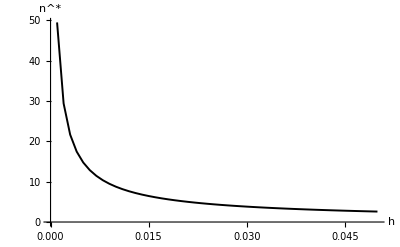

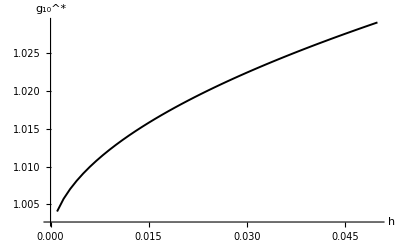

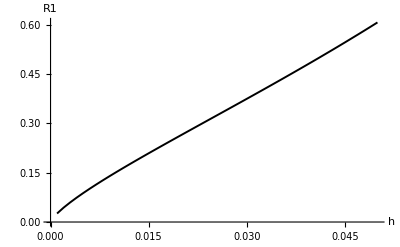

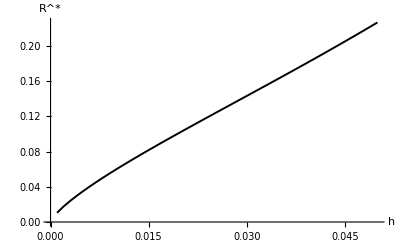

VRdatahtestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdatahtestXZ.xlsx

```mathematica
g1externalh=1.15892+0.01;


RdatahtestXZ=Table[{0,0,0,0,0},{Length[vdatahtestXZ]}];
For[i=1,i<=Length[vdatahtestXZ],i++,Module[{h,g10,n,Rstar},{h,n,g10}=vdatahtestXZ[[i,{1,2,3}]];
R1=vdatahtestXZ[[i,4]];
Rstar=Sqrt[g1externalh-g10]*R1;
RdatahtestXZ[[i]]={h,g10,n,R1,Rstar};
Print[{h,g10,n,R1,Rstar}];]];

VRdatahtestXZ=Select[RdatahtestXZ,#[[2]]>0&];
testhnXZ=ListPlot[VRdatahtestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testhg10XZ=ListPlot[VRdatahtestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhR1XZ=ListLinePlot[VRdatahtestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testhRXZ=ListLinePlot[VRdatahtestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["h",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatahtestXZ.xlsx",VRdatahtestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatahtestXZ.xlsx",VRdatahtestXZ]
```

### 2.2 Relations of g30 and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;h=1/75;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;g12=1;


samplePoints=Subdivide[0.5,1.5,49];
datag30testXZ=Table[{0,0,0,0,0},{ g30,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, g30=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  g30 = ", g30];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datag30testXZ[[k]]={ g30,n,g10,Sqrt[R12]};
Print[{ g30,n,g10,R12}];
k++;]


vdatag30testXZ=Select[datag30testXZ,#[[2]]>0&&#[[3]]>0&];
Maxg10g30testXZ=Max[vdatag30testXZ[[All,3]]]
```

{1.5,5.18976,1.01829,0.0699486}

{1.47959,5.24379,1.01816,0.0683713}

{1.45918,5.29915,1.01803,0.0668108}

{1.43878,5.35588,1.01791,0.0652671}

{1.41837,5.41404,1.01778,0.06374}

{1.39796,5.47368,1.01765,0.0622296}

{1.37755,5.53487,1.01752,0.0607358}

{1.35714,5.59766,1.01739,0.0592586}

{1.33673,5.66213,1.01725,0.0577979}

{1.31633,5.72835,1.01712,0.0563537}

{1.29592,5.79638,1.01698,0.0549261}

{1.27551,5.86632,1.01685,0.0535148}

{1.2551,5.93825,1.01671,0.05212}

{1.23469,6.01226,1.01657,0.0507416}

{1.21429,6.08844,1.01644,0.0493795}

{1.19388,6.16689,1.0163,0.0480338}

{1.17347,6.24773,1.01615,0.0467045}

{1.15306,6.33106,1.01601,0.0453915}

{1.13265,6.41703,1.01587,0.0440948}

{1.11224,6.50574,1.01572,0.0428144}

❌ FindRoot failed at  g30 = 1.09184

{1.07143,6.69201,1.01543,0.0403026}

❌ FindRoot failed at  g30 = 1.05102

{1.03061,6.89114,1.01513,0.037856}

{1.0102,6.99597,1.01498,0.0366571}

❌ FindRoot failed at  g30 = 0.989796

{0.969388,7.21717,1.01467,0.0343084}

{0.94898,7.334,1.01451,0.0331586}

❌ FindRoot failed at  g30 = 0.928571

{0.908163,7.58137,1.0142,0.030908}

{0.887755,7.7125,1.01403,0.0298074}

{0.867347,7.84902,1.01387,0.0287232}

{0.846939,7.99127,1.0137,0.0276555}

{0.826531,8.13966,1.01354,0.0266043}

{0.806122,8.29461,1.01337,0.0255697}

❌ FindRoot failed at  g30 = 0.785714

{0.765306,8.62608,1.01302,0.0235505}

❌ FindRoot failed at  g30 = 0.744898

{0.72449,8.99003,1.01267,0.0215983}

{0.704082,9.18579,1.01249,0.0206475}

{0.683673,9.39174,1.0123,0.0197136}

{0.663265,9.60875,1.01212,0.0187969}

{0.642857,9.83777,1.01193,0.0178973}

{0.622449,10.0799,1.01174,0.017015}

{0.602041,10.3363,1.01154,0.0161501}

{0.581633,10.6084,1.01134,0.0153027}

{0.561224,10.8978,1.01114,0.014473}

{0.540816,11.2062,1.01093,0.0136611}

{0.520408,11.5356,1.01072,0.0128671}

{0.5,11.8885,1.01051,0.0120913}

1.01829

#### Graph

{1.5,1.01829,5.18976,0.264478,0.0980435}

{1.47959,1.01816,5.24379,0.261479,0.0969764}

{1.45918,1.01803,5.29915,0.258478,0.0959076}

{1.43878,1.01791,5.35588,0.255474,0.0948371}

{1.41837,1.01778,5.41404,0.252468,0.0937648}

{1.39796,1.01765,5.47368,0.249459,0.0926908}

{1.37755,1.01752,5.53487,0.246446,0.0916148}

{1.35714,1.01739,5.59766,0.243431,0.0905369}

{1.33673,1.01725,5.66213,0.240412,0.089457}

{1.31633,1.01712,5.72835,0.237389,0.0883749}

{1.29592,1.01698,5.79638,0.234363,0.0872906}

{1.27551,1.01685,5.86632,0.231333,0.086204}

{1.2551,1.01671,5.93825,0.228298,0.085115}

{1.23469,1.01657,6.01226,0.225259,0.0840235}

{1.21429,1.01644,6.08844,0.222215,0.0829295}

{1.19388,1.0163,6.16689,0.219166,0.0818328}

{1.17347,1.01615,6.24773,0.216112,0.0807334}

{1.15306,1.01601,6.33106,0.213053,0.0796311}

{1.13265,1.01587,6.41703,0.209988,0.0785258}

{1.11224,1.01572,6.50574,0.206917,0.0774174}

{1.07143,1.01543,6.69201,0.200755,0.0751909}

{1.03061,1.01513,6.89114,0.194566,0.0729506}

{1.0102,1.01498,6.99597,0.191461,0.071825}

{0.969388,1.01467,7.21717,0.185225,0.069562}

{0.94898,1.01451,7.334,0.182095,0.0684243}

{0.908163,1.0142,7.58137,0.175807,0.0661358}

{0.887755,1.01403,7.7125,0.172648,0.0649847}

{0.867347,1.01387,7.84902,0.169479,0.0638287}

{0.846939,1.0137,7.99127,0.166299,0.0626676}

{0.826531,1.01354,8.13966,0.163108,0.0615013}

{0.806122,1.01337,8.29461,0.159905,0.0603295}

{0.765306,1.01302,8.62608,0.153462,0.0579687}

{0.72449,1.01267,8.99003,0.146963,0.055583}

{0.704082,1.01249,9.18579,0.143692,0.0543801}

{0.683673,1.0123,9.39174,0.140405,0.0531702}

{0.663265,1.01212,9.60875,0.137102,0.0519529}

{0.642857,1.01193,9.83777,0.133781,0.0507279}

{0.622449,1.01174,10.0799,0.130442,0.0494947}

{0.602041,1.01154,10.3363,0.127083,0.048253}

{0.581633,1.01134,10.6084,0.123704,0.0470024}

{0.561224,1.01114,10.8978,0.120304,0.0457423}

{0.540816,1.01093,11.2062,0.116881,0.0444724}

{0.520408,1.01072,11.5356,0.113433,0.0431919}

{0.5,1.01051,11.8885,0.109961,0.0419005}

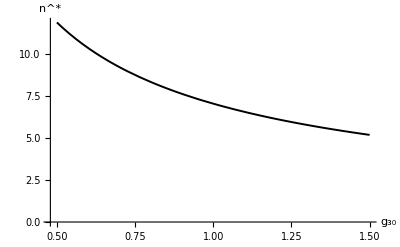

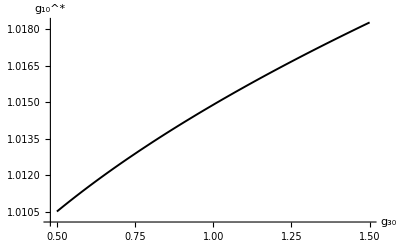

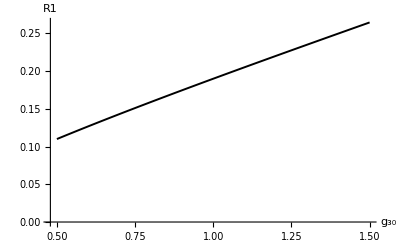

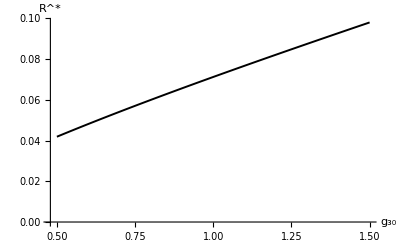

VRdatag30testXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdatag30testXZ.xlsx

```mathematica
g1externalg30=1.14571+0.01;


Rdatag30testXZ=Table[{0,0,0,0,0},{Length[vdatag30testXZ]}];
For[i=1,i<=Length[vdatag30testXZ],i++,Module[{g30,g10,n,Rstar},{g30,n,g10}=vdatag30testXZ[[i,{1,2,3}]];
R1=vdatag30testXZ[[i,4]];
Rstar=Sqrt[g1externalg30-g10]*R1;
Rdatag30testXZ[[i]]={g30,g10,n,R1,Rstar};
Print[{g30,g10,n,R1,Rstar}];]];

VRdatag30testXZ=Select[Rdatag30testXZ,#[[2]]>0&];
testg30nXZ=ListPlot[VRdatag30testXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testg30g10XZ=ListPlot[VRdatag30testXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30R1XZ=ListLinePlot[VRdatag30testXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testg30RXZ=ListLinePlot[VRdatag30testXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["g_30",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatag30testXZ.xlsx",VRdatag30testXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatag30testXZ.xlsx",VRdatag30testXZ]
```

### 2.3 Relations of KK and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;g12=1;
cf=100;phif=0.05;beta=Pi/4;lamdaf=0.885;


samplePoints=E^Subdivide[Log[0.1],Log[0.5],49];
dataKKtestXZ=Table[{0,0,0,0,0},{KK,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.21;
ninit=10.1;

For[i=Length[samplePoints],i>=1,i--,KK=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at KK = ",KK];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataKKtestXZ[[k]]={KK,n,g10,Sqrt[R12]};
Print[{KK,n,g10,R12}];
k++;]


vdataKKtestXZ=Select[dataKKtestXZ,#[[2]]>0&&#[[3]]>0&];
Maxg10KKtestXZ=Max[vdataKKtestXZ[[All,3]]]
```

{0.5,8.81201,1.02369,0.0270668}

{0.483844,8.7424,1.0233,0.0272423}

{0.46821,8.67328,1.02291,0.0274304}

{0.453081,8.60466,1.02253,0.0276308}

{0.438441,8.53653,1.02216,0.027843}

{0.424274,8.4689,1.02179,0.0280669}

{0.410565,8.40175,1.02143,0.0283021}

{0.397299,8.3351,1.02108,0.0285484}

{0.384461,8.26892,1.02073,0.0288058}

{0.372038,8.20324,1.02039,0.0290738}

{0.360017,8.13803,1.02005,0.0293525}

❌ FindRoot failed at KK = 0.348384

{0.337127,8.00905,1.0194,0.0299413}

{0.326234,7.94527,1.01908,0.0302512}

{0.315693,7.88197,1.01876,0.0305713}

❌ FindRoot failed at KK = 0.305492

{0.295621,7.75677,1.01815,0.0312419}

{0.286069,7.69487,1.01785,0.0315923}

{0.276825,7.63343,1.01756,0.0319528}

{0.26788,7.57245,1.01727,0.0323233}

{0.259225,7.51193,1.01699,0.0327038}

{0.250848,7.45186,1.01671,0.0330944}

{0.242743,7.39225,1.01643,0.033495}

❌ FindRoot failed at KK = 0.234899

{0.227309,7.27437,1.0159,0.0343266}

{0.219965,7.2161,1.01563,0.0347575}

{0.212857,7.15827,1.01538,0.0351987}

{0.205979,7.10089,1.01512,0.0356502}

{0.199324,7.04393,1.01488,0.0361119}

{0.192883,6.98742,1.01463,0.0365841}

{0.186651,6.93133,1.01439,0.0370667}

❌ FindRoot failed at KK = 0.180619

{0.174783,6.82045,1.01392,0.0380637}

{0.169136,6.76564,1.01369,0.0385782}

{0.163671,6.71126,1.01347,0.0391036}

❌ FindRoot failed at KK = 0.158382

{0.153264,6.60374,1.01303,0.0401872}

{0.148312,6.55061,1.01282,0.0407457}

{0.14352,6.49788,1.01261,0.0413155}

{0.138882,6.44557,1.0124,0.0418966}

{0.134395,6.39365,1.0122,0.0424893}

❌ FindRoot failed at KK = 0.130052

{0.12585,6.29104,1.0118,0.0437097}

{0.121783,6.24032,1.01161,0.0443378}

{0.117848,6.19001,1.01142,0.0449779}

{0.11404,6.14008,1.01123,0.0456303}

{0.110356,6.09054,1.01104,0.046295}

{0.10679,6.0414,1.01086,0.0469723}

{0.103339,5.99263,1.01069,0.0476624}

{0.1,5.94425,1.01051,0.0483653}

1.02369

#### Graph

{0.5,1.02369,8.81201,0.16452,0.0612477}

{0.483844,1.0233,8.7424,0.165052,0.0615327}

{0.46821,1.02291,8.67328,0.165621,0.0618302}

{0.453081,1.02253,8.60466,0.166225,0.0621398}

{0.438441,1.02216,8.53653,0.166862,0.062461}

{0.424274,1.02179,8.4689,0.167532,0.0627934}

{0.410565,1.02143,8.40175,0.168232,0.0631367}

{0.397299,1.02108,8.3351,0.168963,0.0634904}

{0.384461,1.02073,8.26892,0.169723,0.0638544}

{0.372038,1.02039,8.20324,0.17051,0.0642283}

{0.360017,1.02005,8.13803,0.171326,0.0646118}

{0.337127,1.0194,8.00905,0.173036,0.0654068}

{0.326234,1.01908,7.94527,0.173929,0.0658179}

{0.315693,1.01876,7.88197,0.174846,0.0662378}

{0.295621,1.01815,7.75677,0.176754,0.0671032}

{0.286069,1.01785,7.69487,0.177742,0.0675484}

{0.276825,1.01756,7.63343,0.178753,0.0680018}

{0.26788,1.01727,7.57245,0.179787,0.0684631}

{0.259225,1.01699,7.51193,0.180842,0.0689324}

{0.250848,1.01671,7.45186,0.181919,0.0694094}

{0.242743,1.01643,7.39225,0.183016,0.0698942}

{0.227309,1.0159,7.27437,0.185274,0.0708863}

{0.219965,1.01563,7.2161,0.186434,0.0713936}

{0.212857,1.01538,7.15827,0.187613,0.0719082}

{0.205979,1.01512,7.10089,0.188813,0.07243}

{0.199324,1.01488,7.04393,0.190031,0.0729591}

{0.192883,1.01463,6.98742,0.19127,0.0734954}

{0.186651,1.01439,6.93133,0.192527,0.0740388}

{0.174783,1.01392,6.82045,0.195099,0.0751467}

{0.169136,1.01369,6.76564,0.196413,0.0757112}

{0.163671,1.01347,6.71126,0.197746,0.0762826}

{0.153264,1.01303,6.60374,0.200468,0.0774462}

{0.148312,1.01282,6.55061,0.201856,0.0780383}

{0.14352,1.01261,6.49788,0.203262,0.0786372}

{0.138882,1.0124,6.44557,0.204687,0.0792431}

{0.134395,1.0122,6.39365,0.206129,0.0798557}

{0.12585,1.0118,6.29104,0.209069,0.0811014}

{0.121783,1.01161,6.24032,0.210565,0.0817345}

{0.117848,1.01142,6.19001,0.21208,0.0823744}

{0.11404,1.01123,6.14008,0.213612,0.0830211}

{0.110356,1.01104,6.09054,0.215163,0.0836745}

{0.10679,1.01086,6.0414,0.216731,0.0843348}

{0.103339,1.01069,5.99263,0.218317,0.0850019}

{0.1,1.01051,5.94425,0.219921,0.0856759}

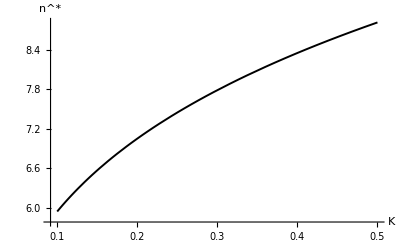

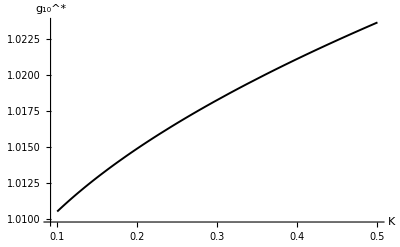

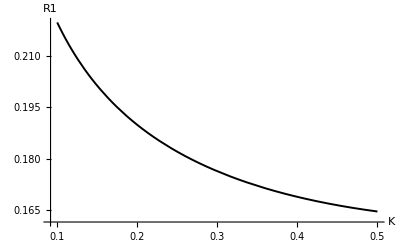

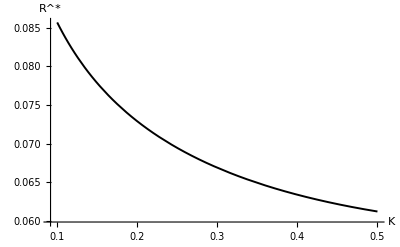

VRdataKKtestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdataKKtestXZ.xlsx

```mathematica
g1externalKK=1.15228+0.01;


RdataKKtestXZ=Table[{0,0,0,0,0},{Length[vdataKKtestXZ]}];
For[i=1,i<=Length[vdataKKtestXZ],i++,Module[{KK,g10,n,Rstar},{KK,n,g10}=vdataKKtestXZ[[i,{1,2,3}]];
R1=vdataKKtestXZ[[i,4]];
Rstar=Sqrt[g1externalKK-g10]*R1;
RdataKKtestXZ[[i]]={KK,g10,n,R1,Rstar};
Print[{KK,g10,n,R1,Rstar}];]];

VRdataKKtestXZ=Select[RdataKKtestXZ,#[[2]]>0&];
testKKnXZ=ListPlot[VRdataKKtestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testKKg10XZ=ListPlot[VRdataKKtestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKR1XZ=ListLinePlot[VRdataKKtestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testKKRXZ=ListLinePlot[VRdataKKtestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["K",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataKKtestXZ.xlsx",VRdataKKtestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdataKKtestXZ.xlsx",VRdataKKtestXZ]
```

## 3. parametric study for skin fiber

### 3.1 Relations of beta and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;KK=0.2;g30=1;h=1.0/75;g12=1;
cf=100;phif=0.05;lamdaf=0.885;


betamin=0;
betamax=Pi/2;
samplePoints=Subdivide[ betamin, betamax,49];
databetatestXZ=Table[{0,0,0,0,0,0},{ beta,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;

g10init=1.193;
ninit=6.492;

For[i=Length[samplePoints],i>=1,i--, beta=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  beta = ", beta];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
databetatestXZ[[k]]={ beta,n,g10,Sqrt[R12]};
Print[{ beta,n,g10,Sqrt[R12]}];
k++;]


vdatabetatestXZ=Select[databetatestXZ,#[[2]]>0&&#[[3]]>0&];
Maxg10betatestXZ=Max[vdatabetatestXZ[[All,3]]]
```

{π/2,6.13514,0.918058,0.217709}

{(24 π)/49,6.14167,0.917957,0.217489}

{(47 π)/98,6.16128,0.917656,0.216968}

{(23 π)/49,6.19404,0.917157,0.216421}

{(45 π)/98,6.24009,0.916463,0.216023}

{(22 π)/49,6.29961,0.915582,0.215749}

{(43 π)/98,6.37276,0.914526,0.21544}

{(3 π)/7,6.45961,0.913316,0.214914}

{(41 π)/98,6.56,0.911984,0.214044}

{(20 π)/49,6.67329,0.910584,0.212778}

{(39 π)/98,6.79807,0.909195,0.211131}

{(19 π)/49,6.93169,0.907937,0.209163}

{(37 π)/98,7.06977,0.906986,0.206956}

{(18 π)/49,7.20576,0.906578,0.204599}

{(5 π)/14,7.33085,0.907022,0.202174}

{(17 π)/49,7.43485,0.908678,0.199765}

{(33 π)/98,7.50805,0.91192,0.197467}

{(16 π)/49,7.54394,0.917065,0.195399}

{(31 π)/98,7.54118,0.924315,0.193678}

{(15 π)/49,7.50388,0.933714,0.192377}

{(29 π)/98,7.43994,0.945157,0.191493}

❌ FindRoot failed at  beta = (2 π)/7

❌ FindRoot failed at  beta = (27 π)/98

{(13 π)/49,7.17762,0.989292,0.190378}

{(25 π)/98,7.09056,1.00622,0.190095}

{(12 π)/49,7.01131,1.02367,0.189668}

{(23 π)/98,6.94206,1.04125,0.189027}

{(11 π)/49,6.88353,1.05855,0.188134}

{(3 π)/14,6.83495,1.07508,0.187005}

{(10 π)/49,6.79387,1.09034,0.185717}

{(19 π)/98,6.75598,1.1038,0.184431}

{(9 π)/49,6.71525,1.11497,0.183388}

{(17 π)/98,6.66494,1.12353,0.182882}

{(8 π)/49,6.59942,1.12935,0.183181}

{(15 π)/98,6.51617,1.13262,0.184428}

{π/7,6.41683,1.13372,0.186589}

{(13 π)/98,6.3063,1.13318,0.189465}

{(6 π)/49,6.19085,1.13154,0.192768}

{(11 π)/98,6.07627,1.12924,0.196198}

{(5 π)/49,5.96702,1.12663,0.199488}

{(9 π)/98,5.86603,1.12397,0.202433}

{(4 π)/49,5.77498,1.1214,0.204902}

{π/14,5.69472,1.11904,0.206856}

{(3 π)/49,5.62552,1.11694,0.208371}

{(5 π)/98,5.56737,1.11514,0.209657}

{(2 π)/49,5.52011,1.11366,0.211027}

{(3 π)/98,5.48356,1.11251,0.21276}

{π/49,5.45754,1.11168,0.214833}

{π/98,5.44196,1.11119,0.216693}

{0,5.43678,1.11102,0.217464}

1.13372

#### Graph

{π/2,0.918058,6.13514,0.217709,0.10521}

{(24 π)/49,0.917957,6.14167,0.217489,0.105127}

{(47 π)/98,0.917656,6.16128,0.216968,0.104942}

{(23 π)/49,0.917157,6.19404,0.216421,0.104789}

{(45 π)/98,0.916463,6.24009,0.216023,0.104752}

{(22 π)/49,0.915582,6.29961,0.215749,0.104815}

{(43 π)/98,0.914526,6.37276,0.21544,0.104898}

{(3 π)/7,0.913316,6.45961,0.214914,0.104909}

{(41 π)/98,0.911984,6.56,0.214044,0.104776}

{(20 π)/49,0.910584,6.67329,0.212778,0.10446}

{(39 π)/98,0.909195,6.79807,0.211131,0.10395}

{(19 π)/49,0.907937,6.93169,0.209163,0.103247}

{(37 π)/98,0.906986,7.06977,0.206956,0.102357}

{(18 π)/49,0.906578,7.20576,0.204599,0.101276}

{(5 π)/14,0.907022,7.33085,0.202174,0.099985}

{(17 π)/49,0.908678,7.43485,0.199765,0.0984583}

{(33 π)/98,0.91192,7.50805,0.197467,0.0966744}

{(16 π)/49,0.917065,7.54394,0.195399,0.0946295}

{(31 π)/98,0.924315,7.54118,0.193678,0.092335}

{(15 π)/49,0.933714,7.50388,0.192377,0.0897985}

{(29 π)/98,0.945157,7.43994,0.191493,0.0870066}

{(13 π)/49,0.989292,7.17762,0.190378,0.0766987}

{(25 π)/98,1.00622,7.09056,0.190095,0.0724811}

{(12 π)/49,1.02367,7.01131,0.189668,0.0678396}

{(23 π)/98,1.04125,6.94206,0.189027,0.0627913}

{(11 π)/49,1.05855,6.88353,0.188134,0.0573884}

{(3 π)/14,1.07508,6.83495,0.187005,0.0517282}

{(10 π)/49,1.09034,6.79387,0.185717,0.0459655}

{(19 π)/98,1.1038,6.75598,0.184431,0.0403233}

{(9 π)/49,1.11497,6.71525,0.183388,0.0350973}

{(17 π)/98,1.12353,6.66494,0.182882,0.0306417}

{(8 π)/49,1.12935,6.59942,0.183181,0.0273214}

{(15 π)/98,1.13262,6.51617,0.184428,0.0254088}

{π/7,1.13372,6.41683,0.186589,0.024949}

{(13 π)/98,1.13318,6.3063,0.189465,0.0257111}

{(6 π)/49,1.13154,6.19085,0.192768,0.0273031}

{(11 π)/98,1.12924,6.07627,0.196198,0.0293384}

{(5 π)/49,1.12663,5.96702,0.199488,0.0315207}

{(9 π)/98,1.12397,5.86603,0.202433,0.0336513}

{(4 π)/49,1.1214,5.77498,0.204902,0.0356083}

{π/14,1.11904,5.69472,0.206856,0.0373275}

{(3 π)/49,1.11694,5.62552,0.208371,0.0387932}

{(5 π)/98,1.11514,5.56737,0.209657,0.0400324}

{(2 π)/49,1.11366,5.52011,0.211027,0.0411039}

{(3 π)/98,1.11251,5.48356,0.21276,0.0420669}

{π/49,1.11168,5.45754,0.214833,0.0429223}

{π/98,1.11119,5.44196,0.216693,0.0435612}

{0,1.11102,5.43678,0.217464,0.0438052}

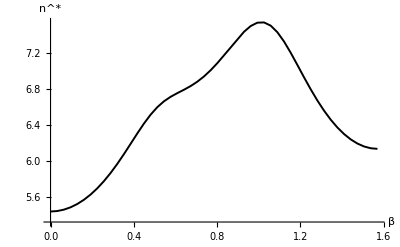

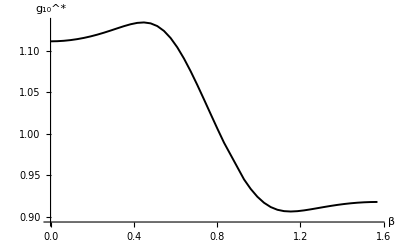

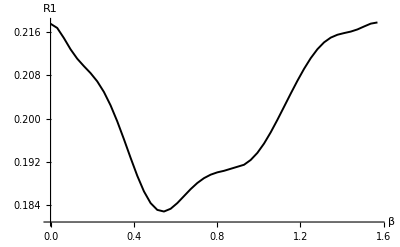

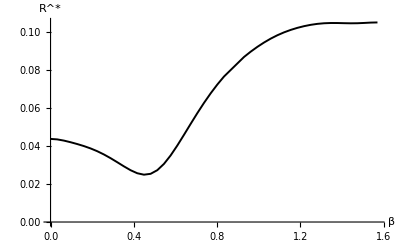

VRdatabetatestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdatabetatestXZ.xlsx

```mathematica
g1externalbeta=1.1416+0.01;


RdatabetatestXZ=Table[{0,0,0,0,0},{Length[vdatabetatestXZ]}];
For[i=1,i<=Length[vdatabetatestXZ],i++,Module[{beta,g10,n,Rstar},{beta,n,g10}=vdatabetatestXZ[[i,{1,2,3}]];
R1=vdatabetatestXZ[[i,4]];
Rstar=Sqrt[g1externalbeta-g10]*R1;
RdatabetatestXZ[[i]]={beta,g10,n,R1,Rstar};
Print[{beta,g10,n,R1,Rstar}];]];

VRdatabetatestXZ=Select[RdatabetatestXZ,#[[2]]>0&];
testbetanXZ=ListPlot[VRdatabetatestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testbetag10XZ=ListPlot[VRdatabetatestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaR1XZ=ListLinePlot[VRdatabetatestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testbetaRXZ=ListLinePlot[VRdatabetatestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["β",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatabetatestXZ.xlsx",VRdatabetatestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatabetatestXZ.xlsx",VRdatabetatestXZ]
```

### 3.2 Relations of lamdaf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;h=1/75;g30=1;KK=0.2;g12=1;
cf=100;phif=0.05;beta=Pi/4;


samplePoints=Subdivide[0.1,1,50];

datalamdaftestXZ=Table[{0,0,0,0,0},{ lamdaf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, lamdaf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  lamdaf = ", lamdaf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datalamdaftestXZ[[k]]={ lamdaf,n,g10,Sqrt[R12]};
Print[{ lamdaf,n,g10,R12}];
k++;]


vdatalamdaftestXZ=Select[datalamdaftestXZ,#[[2]]>0&&#[[3]]>0&];
MaxlamdaftestXZ=Max[vdatalamdaftestXZ[[All,3]]]
```

{1.,8.47237,1.02192,0.0307395}

{0.982,8.13206,1.02008,0.030867}

{0.964,7.85483,1.01866,0.0315887}

{0.946,7.62303,1.01753,0.0325349}

{0.928,7.4253,1.01659,0.0335651}

{0.91,7.25393,1.01581,0.0346175}

{0.892,7.10351,1.01514,0.0356627}

{0.874,6.9701,1.01456,0.0366862}

{0.856,6.85072,1.01405,0.0376806}

{0.838,6.74313,1.0136,0.0386427}

{0.82,6.64554,1.0132,0.039571}

{0.802,6.55655,1.01284,0.0404654}

{0.784,6.47502,1.01251,0.0413264}

{0.766,6.40002,1.01222,0.0421548}

❌ FindRoot failed at  lamdaf = 0.748

{0.73,6.26667,1.0117,0.0437178}

{0.712,6.20713,1.01148,0.0444546}

❌ FindRoot failed at  lamdaf = 0.694

{0.676,6.10003,1.01108,0.0458437}

❌ FindRoot failed at  lamdaf = 0.658

{0.64,6.0065,1.01073,0.0471269}

{0.622,5.96412,1.01058,0.047731}

{0.604,5.92434,1.01044,0.0483113}

{0.586,5.88697,1.0103,0.0488683}

{0.568,5.85183,1.01018,0.049403}

{0.55,5.81877,1.01006,0.0499158}

{0.532,5.78764,1.00995,0.0504075}

{0.514,5.75833,1.00985,0.0508785}

{0.496,5.73072,1.00975,0.0513294}

{0.478,5.70471,1.00966,0.0517607}

{0.46,5.68022,1.00958,0.0521728}

{0.442,5.65715,1.0095,0.0525662}

{0.424,5.63544,1.00943,0.0529413}

{0.406,5.61502,1.00936,0.0532984}

{0.388,5.59582,1.00929,0.0536379}

{0.37,5.5778,1.00923,0.05396}

{0.352,5.5609,1.00918,0.0542651}

{0.334,5.54508,1.00912,0.0545535}

{0.316,5.5303,1.00907,0.0548254}

{0.298,5.51651,1.00903,0.0550811}

{0.28,5.50369,1.00898,0.0553207}

{0.262,5.49181,1.00894,0.0555445}

{0.244,5.48082,1.00891,0.0557526}

{0.226,5.47072,1.00888,0.0559453}

{0.208,5.46147,1.00884,0.0561226}

{0.19,5.45306,1.00882,0.0562847}

{0.172,5.44546,1.00879,0.0564318}

{0.154,5.43867,1.00877,0.0565639}

{0.136,5.43266,1.00875,0.0566812}

{0.118,5.42743,1.00873,0.0567837}

{0.1,5.42295,1.00872,0.0568716}

1.02192

#### Graph

{1.,1.02192,8.47237,0.175327,0.122969}

{0.982,1.02008,8.13206,0.17569,0.123454}

{0.964,1.01866,7.85483,0.177732,0.125068}

{0.946,1.01753,7.62303,0.180374,0.127073}

{0.928,1.01659,7.4253,0.183208,0.12919}

{0.91,1.01581,7.25393,0.186058,0.131304}

{0.892,1.01514,7.10351,0.188846,0.133361}

{0.874,1.01456,6.9701,0.191536,0.13534}

{0.856,1.01405,6.85072,0.194115,0.137232}

{0.838,1.0136,6.74313,0.196577,0.139035}

{0.82,1.0132,6.64554,0.198925,0.140751}

{0.802,1.01284,6.55655,0.20116,0.142384}

{0.784,1.01251,6.47502,0.203289,0.143938}

{0.766,1.01222,6.40002,0.205316,0.145416}

{0.73,1.0117,6.26667,0.209088,0.148163}

{0.712,1.01148,6.20713,0.210842,0.14944}

{0.676,1.01108,6.10003,0.214111,0.151817}

{0.64,1.01073,6.0065,0.217087,0.15398}

{0.622,1.01058,5.96412,0.218474,0.154988}

{0.604,1.01044,5.92434,0.219798,0.155949}

{0.586,1.0103,5.88697,0.221062,0.156866}

{0.568,1.01018,5.85183,0.222268,0.157742}

{0.55,1.01006,5.81877,0.223418,0.158577}

{0.532,1.00995,5.78764,0.224516,0.159373}

{0.514,1.00985,5.75833,0.225563,0.160132}

{0.496,1.00975,5.73072,0.22656,0.160855}

{0.478,1.00966,5.70471,0.22751,0.161544}

{0.46,1.00958,5.68022,0.228414,0.1622}

{0.442,1.0095,5.65715,0.229273,0.162823}

{0.424,1.00943,5.63544,0.23009,0.163415}

{0.406,1.00936,5.61502,0.230864,0.163976}

{0.388,1.00929,5.59582,0.231598,0.164508}

{0.37,1.00923,5.5778,0.232293,0.165011}

{0.352,1.00918,5.5609,0.232949,0.165486}

{0.334,1.00912,5.54508,0.233567,0.165934}

{0.316,1.00907,5.5303,0.234148,0.166355}

{0.298,1.00903,5.51651,0.234694,0.16675}

{0.28,1.00898,5.50369,0.235204,0.16712}

{0.262,1.00894,5.49181,0.235679,0.167464}

{0.244,1.00891,5.48082,0.23612,0.167783}

{0.226,1.00888,5.47072,0.236528,0.168078}

{0.208,1.00884,5.46147,0.236902,0.16835}

{0.19,1.00882,5.45306,0.237244,0.168597}

{0.172,1.00879,5.44546,0.237554,0.168822}

{0.154,1.00877,5.43867,0.237832,0.169023}

{0.136,1.00875,5.43266,0.238078,0.169201}

{0.118,1.00873,5.42743,0.238293,0.169357}

{0.1,1.00872,5.42295,0.238478,0.169491}

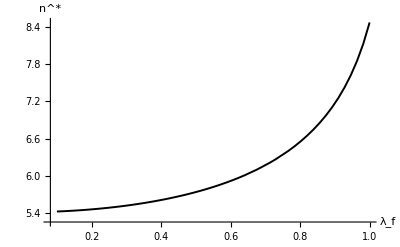

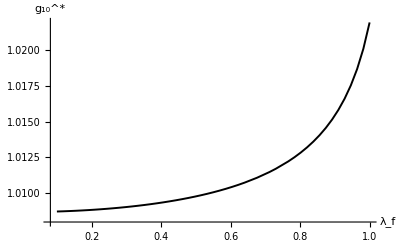

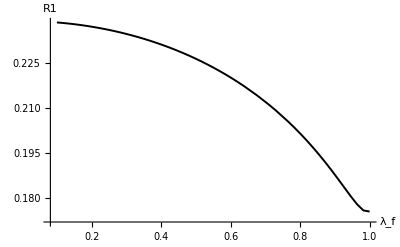

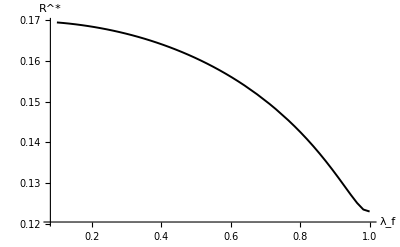

VRdatalamdaftestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdatalamdaftestXZ.xlsx

```mathematica
g1externallamdaf=1.50384+0.01;


RdatalamdaftestXZ=Table[{0,0,0,0,0},{Length[vdatalamdaftestXZ]}];
For[i=1,i<=Length[vdatalamdaftestXZ],i++,Module[{lamdaf,g10,n,Rstar},{lamdaf,n,g10}=vdatalamdaftestXZ[[i,{1,2,3}]];
R1=vdatalamdaftestXZ[[i,4]];
Rstar=Sqrt[g1externallamdaf-g10]*R1;
RdatalamdaftestXZ[[i]]={lamdaf,g10,n,R1,Rstar};
Print[{lamdaf,g10,n,R1,Rstar}];]];

VRdatalamdaftestXZ=Select[RdatalamdaftestXZ,#[[2]]>0&];
testlamdafnXZ=ListPlot[VRdatalamdaftestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testlamdafg10XZ=ListPlot[VRdatalamdaftestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafR1XZ=ListLinePlot[VRdatalamdaftestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testlamdafRXZ=ListLinePlot[VRdatalamdaftestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["λ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatalamdaftestXZ.xlsx",VRdatalamdaftestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatalamdaftestXZ.xlsx",VRdatalamdaftestXZ]
```

### 3.3 Relations of cf and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
phif=0.05;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[50,100,100];
datacftestXZ=Table[{0,0,0,0,0},{ cf,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, cf=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  cf = ", cf];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
datacftestXZ[[k]]={ cf,n,g10,Sqrt[R12]};
Print[{ cf,n,g10,R12}];
k++;]


vdatacftestXZ=Select[datacftestXZ,#[[2]]>0&&#[[3]]>0&];
MaxcftestXZ=Max[vdatacftestXZ[[All,3]]]
```

{100,7.04979,1.0149,0.0360638}

{199/2,7.05441,1.01492,0.0360235}

{99,7.05905,1.01494,0.0359831}

{197/2,7.06371,1.01496,0.0359427}

{98,7.06838,1.01498,0.0359022}

{195/2,7.07307,1.015,0.0358616}

{97,7.07777,1.01502,0.035821}

{193/2,7.08249,1.01504,0.0357803}

{96,7.08722,1.01506,0.0357396}

{191/2,7.09197,1.01509,0.0356988}

{95,7.09674,1.01511,0.035658}

{189/2,7.10152,1.01513,0.0356171}

{94,7.10632,1.01515,0.0355761}

{187/2,7.11114,1.01517,0.0355351}

{93,7.11597,1.01519,0.035494}

{185/2,7.12082,1.01521,0.0354529}

{92,7.12568,1.01523,0.0354117}

{183/2,7.13056,1.01525,0.0353704}

{91,7.13546,1.01528,0.0353291}

{181/2,7.14038,1.0153,0.0352877}

{90,7.14531,1.01532,0.0352463}

{179/2,7.15026,1.01534,0.0352048}

{89,7.15523,1.01536,0.0351632}

{177/2,7.16022,1.01538,0.0351216}

{88,7.16522,1.01541,0.0350799}

{175/2,7.17024,1.01543,0.0350382}

{87,7.17528,1.01545,0.0349963}

{173/2,7.18033,1.01547,0.0349545}

{86,7.18541,1.0155,0.0349125}

{171/2,7.1905,1.01552,0.0348705}

{85,7.19561,1.01554,0.0348284}

{169/2,7.20074,1.01556,0.0347863}

{84,7.20589,1.01559,0.0347441}

{167/2,7.21106,1.01561,0.0347018}

{83,7.21624,1.01563,0.0346595}

{165/2,7.22144,1.01566,0.0346171}

{82,7.22667,1.01568,0.0345746}

{163/2,7.23191,1.0157,0.0345321}

{81,7.23717,1.01573,0.0344895}

{161/2,7.24245,1.01575,0.0344468}

{80,7.24775,1.01577,0.0344041}

{159/2,7.25307,1.0158,0.0343612}

{79,7.25841,1.01582,0.0343184}

{157/2,7.26377,1.01584,0.0342754}

{78,7.26915,1.01587,0.0342324}

{155/2,7.27455,1.01589,0.0341893}

{77,7.27997,1.01592,0.0341461}

{153/2,7.28541,1.01594,0.0341029}

{76,7.29087,1.01597,0.0340596}

{151/2,7.29636,1.01599,0.0340162}

{75,7.30186,1.01602,0.0339727}

{149/2,7.30738,1.01604,0.0339292}

{74,7.31293,1.01607,0.0338855}

{147/2,7.31849,1.01609,0.0338419}

{73,7.32408,1.01612,0.0337981}

{145/2,7.32969,1.01614,0.0337542}

{72,7.33532,1.01617,0.0337103}

{143/2,7.34098,1.01619,0.0336663}

{71,7.34665,1.01622,0.0336222}

{141/2,7.35235,1.01624,0.0335781}

{70,7.35807,1.01627,0.0335338}

{139/2,7.36381,1.0163,0.0334895}

{69,7.36958,1.01632,0.0334451}

{137/2,7.37536,1.01635,0.0334006}

{68,7.38117,1.01638,0.0333561}

{135/2,7.38701,1.0164,0.0333114}

{67,7.39287,1.01643,0.0332667}

{133/2,7.39875,1.01646,0.0332218}

{66,7.40465,1.01648,0.0331769}

{131/2,7.41058,1.01651,0.0331319}

{65,7.41653,1.01654,0.0330869}

{129/2,7.42251,1.01656,0.0330417}

{64,7.42851,1.01659,0.0329964}

{127/2,7.43454,1.01662,0.0329511}

{63,7.44059,1.01665,0.0329056}

{125/2,7.44667,1.01668,0.0328601}

{62,7.45277,1.0167,0.0328145}

{123/2,7.45889,1.01673,0.0327687}

{61,7.46505,1.01676,0.0327229}

{121/2,7.47122,1.01679,0.032677}

{60,7.47743,1.01682,0.032631}

{119/2,7.48366,1.01685,0.0325849}

{59,7.48991,1.01687,0.0325387}

{117/2,7.4962,1.0169,0.0324924}

{58,7.5025,1.01693,0.032446}

{115/2,7.50884,1.01696,0.0323995}

{57,7.5152,1.01699,0.0323529}

{113/2,7.5216,1.01702,0.0323062}

{56,7.52801,1.01705,0.0322593}

{111/2,7.53446,1.01708,0.0322124}

{55,7.54093,1.01711,0.0321654}

{109/2,7.54744,1.01714,0.0321182}

{54,7.55397,1.01717,0.032071}

{107/2,7.56053,1.0172,0.0320236}

{53,7.56711,1.01723,0.0319761}

{105/2,7.57373,1.01727,0.0319285}

{52,7.58038,1.0173,0.0318808}

{103/2,7.58705,1.01733,0.031833}

{51,7.59376,1.01736,0.031785}

{101/2,7.6005,1.01739,0.031737}

{50,7.60726,1.01742,0.0316888}

1.01742

#### Graph

{100,1.0149,7.04979,0.189905,0.070213}

{199/2,1.01492,7.05441,0.189799,0.0701686}

{99,1.01494,7.05905,0.189692,0.0701241}

{197/2,1.01496,7.06371,0.189586,0.0700795}

{98,1.01498,7.06838,0.189479,0.0700348}

{195/2,1.015,7.07307,0.189372,0.06999}

{97,1.01502,7.07777,0.189264,0.0699451}

{193/2,1.01504,7.08249,0.189157,0.0699001}

{96,1.01506,7.08722,0.189049,0.069855}

{191/2,1.01509,7.09197,0.188941,0.0698099}

{95,1.01511,7.09674,0.188833,0.0697646}

{189/2,1.01513,7.10152,0.188725,0.0697192}

{94,1.01515,7.10632,0.188616,0.0696738}

{187/2,1.01517,7.11114,0.188508,0.0696282}

{93,1.01519,7.11597,0.188399,0.0695826}

{185/2,1.01521,7.12082,0.188289,0.0695368}

{92,1.01523,7.12568,0.18818,0.069491}

{183/2,1.01525,7.13056,0.18807,0.069445}

{91,1.01528,7.13546,0.18796,0.069399}

{181/2,1.0153,7.14038,0.18785,0.0693528}

{90,1.01532,7.14531,0.18774,0.0693066}

{179/2,1.01534,7.15026,0.187629,0.0692602}

{89,1.01536,7.15523,0.187519,0.0692138}

{177/2,1.01538,7.16022,0.187408,0.0691672}

{88,1.01541,7.16522,0.187296,0.0691206}

{175/2,1.01543,7.17024,0.187185,0.0690738}

{87,1.01545,7.17528,0.187073,0.0690269}

{173/2,1.01547,7.18033,0.186961,0.06898}

{86,1.0155,7.18541,0.186849,0.0689329}

{171/2,1.01552,7.1905,0.186736,0.0688857}

{85,1.01554,7.19561,0.186624,0.0688384}

{169/2,1.01556,7.20074,0.186511,0.068791}

{84,1.01559,7.20589,0.186398,0.0687435}

{167/2,1.01561,7.21106,0.186284,0.0686959}

{83,1.01563,7.21624,0.186171,0.0686481}

{165/2,1.01566,7.22144,0.186057,0.0686003}

{82,1.01568,7.22667,0.185943,0.0685523}

{163/2,1.0157,7.23191,0.185828,0.0685042}

{81,1.01573,7.23717,0.185713,0.0684561}

{161/2,1.01575,7.24245,0.185599,0.0684078}

{80,1.01577,7.24775,0.185483,0.0683593}

{159/2,1.0158,7.25307,0.185368,0.0683108}

{79,1.01582,7.25841,0.185252,0.0682622}

{157/2,1.01584,7.26377,0.185136,0.0682134}

{78,1.01587,7.26915,0.18502,0.0681645}

{155/2,1.01589,7.27455,0.184903,0.0681155}

{77,1.01592,7.27997,0.184787,0.0680664}

{153/2,1.01594,7.28541,0.18467,0.0680172}

{76,1.01597,7.29087,0.184552,0.0679678}

{151/2,1.01599,7.29636,0.184435,0.0679183}

{75,1.01602,7.30186,0.184317,0.0678687}

{149/2,1.01604,7.30738,0.184199,0.067819}

{74,1.01607,7.31293,0.18408,0.0677691}

{147/2,1.01609,7.31849,0.183962,0.0677192}

{73,1.01612,7.32408,0.183843,0.067669}

{145/2,1.01614,7.32969,0.183723,0.0676188}

{72,1.01617,7.33532,0.183604,0.0675684}

{143/2,1.01619,7.34098,0.183484,0.0675179}

{71,1.01622,7.34665,0.183364,0.0674673}

{141/2,1.01624,7.35235,0.183243,0.0674166}

{70,1.01627,7.35807,0.183122,0.0673657}

{139/2,1.0163,7.36381,0.183001,0.0673146}

{69,1.01632,7.36958,0.18288,0.0672635}

{137/2,1.01635,7.37536,0.182758,0.0672122}

{68,1.01638,7.38117,0.182636,0.0671608}

{135/2,1.0164,7.38701,0.182514,0.0671092}

{67,1.01643,7.39287,0.182392,0.0670575}

{133/2,1.01646,7.39875,0.182269,0.0670056}

{66,1.01648,7.40465,0.182145,0.0669536}

{131/2,1.01651,7.41058,0.182022,0.0669015}

{65,1.01654,7.41653,0.181898,0.0668492}

{129/2,1.01656,7.42251,0.181774,0.0667968}

{64,1.01659,7.42851,0.181649,0.0667442}

{127/2,1.01662,7.43454,0.181524,0.0666915}

{63,1.01665,7.44059,0.181399,0.0666386}

{125/2,1.01668,7.44667,0.181274,0.0665856}

{62,1.0167,7.45277,0.181148,0.0665324}

{123/2,1.01673,7.45889,0.181021,0.0664791}

{61,1.01676,7.46505,0.180895,0.0664256}

{121/2,1.01679,7.47122,0.180768,0.066372}

{60,1.01682,7.47743,0.180641,0.0663182}

{119/2,1.01685,7.48366,0.180513,0.0662642}

{59,1.01687,7.48991,0.180385,0.0662101}

{117/2,1.0169,7.4962,0.180256,0.0661559}

{58,1.01693,7.5025,0.180128,0.0661014}

{115/2,1.01696,7.50884,0.179999,0.0660468}

{57,1.01699,7.5152,0.179869,0.065992}

{113/2,1.01702,7.5216,0.179739,0.0659371}

{56,1.01705,7.52801,0.179609,0.065882}

{111/2,1.01708,7.53446,0.179478,0.0658267}

{55,1.01711,7.54093,0.179347,0.0657712}

{109/2,1.01714,7.54744,0.179216,0.0657156}

{54,1.01717,7.55397,0.179084,0.0656598}

{107/2,1.0172,7.56053,0.178951,0.0656038}

{53,1.01723,7.56711,0.178819,0.0655476}

{105/2,1.01727,7.57373,0.178686,0.0654913}

{52,1.0173,7.58038,0.178552,0.0654347}

{103/2,1.01733,7.58705,0.178418,0.065378}

{51,1.01736,7.59376,0.178284,0.065321}

{101/2,1.01739,7.6005,0.178149,0.0652639}

{50,1.01742,7.60726,0.178013,0.0652066}

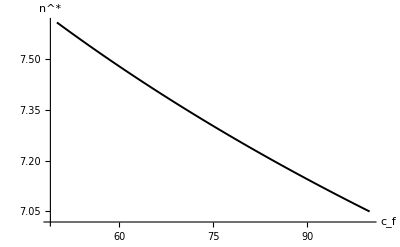

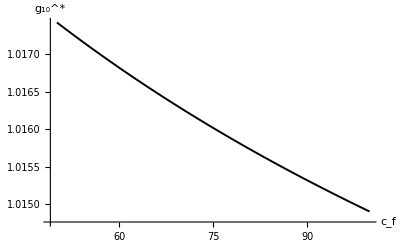

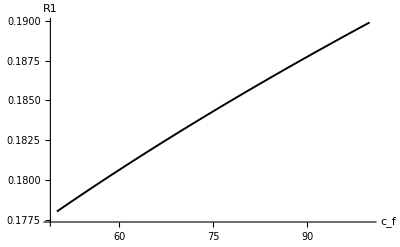

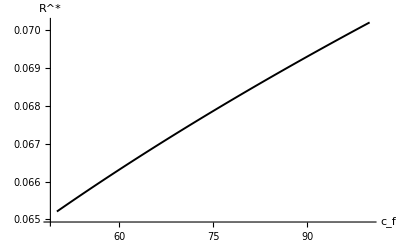

VRdatacftestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdatacftestXZ.xlsx

```mathematica
g1externalcf=1.1416+0.01;


RdatacftestXZ=Table[{0,0,0,0,0},{Length[vdatacftestXZ]}];
For[i=1,i<=Length[vdatacftestXZ],i++,Module[{cf,g10,n,Rstar},{cf,n,g10}=vdatacftestXZ[[i,{1,2,3}]];
R1=vdatacftestXZ[[i,4]];
Rstar=Sqrt[g1externalcf-g10]*R1;
RdatacftestXZ[[i]]={cf,g10,n,R1,Rstar};
Print[{cf,g10,n,R1,Rstar}];]];

VRdatacftestXZ=Select[RdatacftestXZ,#[[2]]>0&];
testcfnXZ=ListPlot[VRdatacftestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testcfg10XZ=ListPlot[VRdatacftestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfR1XZ=ListLinePlot[VRdatacftestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testcfRXZ=ListLinePlot[VRdatacftestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["c_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdatacftestXZ.xlsx",VRdatacftestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatacftestXZ.xlsx",VRdatacftestXZ]
```

### 3.4 Relations of phif and R1

#### test

```mathematica
Clear[c0,cf,KK,h,phim,phif,lamdaf,beta,g10,g30,g12,n,R12,Maxg10,g1external,dparital];

phim=1-phif;

c0=1;g30=1;KK=0.2;g12=1;
cf=100;beta=Pi/4;h=1/75;lamdaf=0.885;

samplePoints=Subdivide[0,0.1,50];
dataphiftestXZ=Table[{0,0,0,0,0},{ phif,samplePoints}];
CriticalCondition=ϕ0-ϕ1*((n*Pi)/2)^2+ϕ2*((n*Pi)/2)^4;
k=1;
dparital=D[CriticalCondition,n]//Simplify;


g10init=1.02;
ninit=8.54;

For[i=Length[samplePoints],i>=1,i--, phif=samplePoints[[i]];
sol=Quiet@Check[FindRoot[{CriticalCondition==0,dparital==0},{{g10,g10init},{n,ninit}},MaxIterations->500,AccuracyGoal->10,PrecisionGoal->8],$Failed];
If[sol===$Failed,Print["❌ FindRoot failed at  phif = ", phif];
Continue[];];
g10=g10/. sol;
n=n/. sol;
g10init=g10;
ninit=n;
R12=(Solve[amplitude==0,R1R1])[[1,1,2]];
dataphiftestXZ[[k]]={ phif,n,g10,Sqrt[R12]};
Print[{ phif,n,g10,R12}];
k++;]


vdataphiftestXZ=Select[dataphiftestXZ,#[[2]]>0&&#[[3]]>0&];
MaxphiftestXZ=Max[vdataphiftestXZ[[All,3]]]
```

{0.1,6.37152,1.01212,0.0430037}

{0.098,6.39286,1.0122,0.0427504}

{0.096,6.41457,1.01228,0.0424955}

{0.094,6.43666,1.01237,0.0422389}

{0.092,6.45913,1.01246,0.0419806}

{0.09,6.48201,1.01255,0.0417205}

{0.088,6.5053,1.01264,0.0414586}

{0.086,6.52901,1.01273,0.0411948}

{0.084,6.55317,1.01283,0.0409291}

{0.082,6.57778,1.01293,0.0406615}

{0.08,6.60287,1.01303,0.0403919}

{0.078,6.62845,1.01313,0.0401202}

{0.076,6.65453,1.01324,0.0398464}

{0.074,6.68114,1.01335,0.0395705}

{0.072,6.7083,1.01346,0.0392923}

{0.07,6.73602,1.01357,0.0390118}

{0.068,6.76433,1.01369,0.038729}

{0.066,6.79325,1.01381,0.0384437}

{0.064,6.8228,1.01394,0.0381559}

{0.062,6.85301,1.01406,0.0378656}

{0.06,6.88391,1.01419,0.0375726}

{0.058,6.91553,1.01433,0.0372768}

{0.056,6.94789,1.01446,0.0369781}

{0.054,6.98103,1.01461,0.0366765}

{0.052,7.01498,1.01475,0.0363718}

{0.05,7.04979,1.0149,0.0360638}

{0.048,7.08548,1.01506,0.0357526}

{0.046,7.12211,1.01522,0.0354378}

{0.044,7.15971,1.01538,0.0351194}

{0.042,7.19834,1.01555,0.0347972}

{0.04,7.23804,1.01573,0.034471}

{0.038,7.27888,1.01591,0.0341405}

{0.036,7.3209,1.0161,0.0338055}

{0.034,7.36418,1.0163,0.0334658}

{0.032,7.40879,1.0165,0.0331209}

{0.03,7.4548,1.01671,0.0327706}

{0.028,7.50228,1.01693,0.0324143}

{0.026,7.55134,1.01716,0.0320514}

{0.024,7.60206,1.0174,0.0316813}

{0.022,7.65455,1.01765,0.0313031}

{0.02,7.70892,1.0179,0.0309155}

{0.018,7.7653,1.01818,0.030517}

{0.016,7.82382,1.01846,0.0301053}

❌ FindRoot failed at  phif = 0.014

{0.012,7.94788,1.01907,0.0292277}

❌ FindRoot failed at  phif = 0.01

{0.008,8.08245,1.01974,0.0282306}

{0.006,8.15413,1.02011,0.0276507}

{0.004,8.22901,1.0205,0.0269746}

{0.002,8.30725,1.02091,0.0261387}

{0.,8.38891,1.02135,0.0250261}

1.02135

#### Graph

{0.1,1.01212,6.37152,0.207373,0.089818}

{0.098,1.0122,6.39286,0.206762,0.0895333}

{0.096,1.01228,6.41457,0.206144,0.0892458}

{0.094,1.01237,6.43666,0.205521,0.0889554}

{0.092,1.01246,6.45913,0.204892,0.088662}

{0.09,1.01255,6.48201,0.204256,0.0883656}

{0.088,1.01264,6.5053,0.203614,0.0880661}

{0.086,1.01273,6.52901,0.202965,0.0877633}

{0.084,1.01283,6.55317,0.20231,0.0874573}

{0.082,1.01293,6.57778,0.201647,0.0871479}

{0.08,1.01303,6.60287,0.200977,0.0868349}

{0.078,1.01313,6.62845,0.2003,0.0865184}

{0.076,1.01324,6.65453,0.199616,0.0861982}

{0.074,1.01335,6.68114,0.198923,0.0858742}

{0.072,1.01346,6.7083,0.198223,0.0855463}

{0.07,1.01357,6.73602,0.197514,0.0852143}

{0.068,1.01369,6.76433,0.196797,0.0848781}

{0.066,1.01381,6.79325,0.196071,0.0845377}

{0.064,1.01394,6.8228,0.195335,0.0841927}

{0.062,1.01406,6.85301,0.194591,0.0838432}

{0.06,1.01419,6.88391,0.193836,0.0834888}

{0.058,1.01433,6.91553,0.193072,0.0831296}

{0.056,1.01446,6.94789,0.192297,0.0827651}

{0.054,1.01461,6.98103,0.191511,0.0823953}

{0.052,1.01475,7.01498,0.190714,0.08202}

{0.05,1.0149,7.04979,0.189905,0.0816388}

{0.048,1.01506,7.08548,0.189084,0.0812516}

{0.046,1.01522,7.12211,0.188249,0.0808581}

{0.044,1.01538,7.15971,0.187402,0.080458}

{0.042,1.01555,7.19834,0.18654,0.080051}

{0.04,1.01573,7.23804,0.185664,0.0796366}

{0.038,1.01591,7.27888,0.184771,0.0792146}

{0.036,1.0161,7.3209,0.183863,0.0787845}

{0.034,1.0163,7.36418,0.182937,0.0783457}

{0.032,1.0165,7.40879,0.181992,0.0778978}

{0.03,1.01671,7.4548,0.181026,0.07744}

{0.028,1.01693,7.50228,0.18004,0.0769716}

{0.026,1.01716,7.55134,0.179029,0.0764918}

{0.024,1.0174,7.60206,0.177993,0.0759993}

{0.022,1.01765,7.65455,0.176927,0.0754929}

{0.02,1.0179,7.70892,0.175828,0.0749707}

{0.018,1.01818,7.7653,0.174691,0.0744305}

{0.016,1.01846,7.82382,0.173509,0.073869}

{0.012,1.01907,7.94788,0.170961,0.072662}

{0.008,1.01974,8.08245,0.16802,0.0712783}

{0.006,1.02011,8.15413,0.166285,0.0704706}

{0.004,1.0205,8.22901,0.164239,0.0695286}

{0.002,1.02091,8.30725,0.161675,0.068364}

{0.,1.02135,8.38891,0.158196,0.0668107}

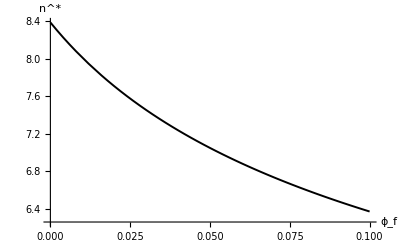

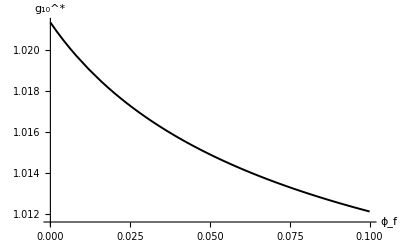

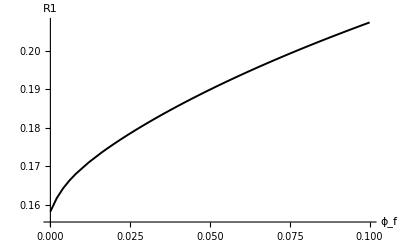

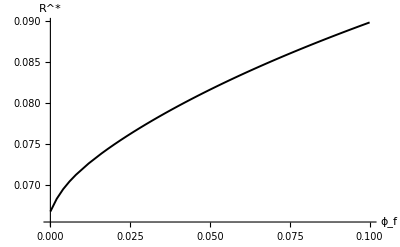

VRdataphiftestXZ.xlsx

E:\June\draft8 -check\Section 4\4. XY_data & XZ_data & YZ_data\4.2 XZ_data\VRdataphiftestXZ.xlsx

```mathematica
g1externalphif=1.18971+0.01;


RdataphiftestXZ=Table[{0,0,0,0,0},{Length[vdataphiftestXZ]}];
For[i=1,i<=Length[vdataphiftestXZ],i++,Module[{phif,g10,n,Rstar},{phif,n,g10}=vdataphiftestXZ[[i,{1,2,3}]];
R1=vdataphiftestXZ[[i,4]];
Rstar=Sqrt[g1externalphif-g10]*R1;
RdataphiftestXZ[[i]]={phif,g10,n,R1,Rstar};
Print[{phif,g10,n,R1,Rstar}];]];

VRdataphiftestXZ=Select[RdataphiftestXZ,#[[2]]>0&];
testphifnXZ=ListPlot[VRdataphiftestXZ[[All,{1,3}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"n^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]

testphifg10XZ=ListPlot[VRdataphiftestXZ[[All,{1,2}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"g_10^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifR1XZ=ListLinePlot[VRdataphiftestXZ[[All,{1,4}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R1"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
testphifRXZ=ListLinePlot[VRdataphiftestXZ[[All,{1,5}]],Joined->True,PlotRange->All,PlotStyle->{Black,Thickness[0.0035]},AxesLabel->{Style["ϕ_f",15],"R^*"},TicksStyle->Directive[FontSize->12,Black],AxesStyle->Directive[FontSize->15,Black]]
Export["VRdataphiftestXZ.xlsx",VRdataphiftestXZ]
Export["E:\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdataphiftestXZ.xlsx",VRdataphiftestXZ]
```